```mathematica
SetDirectory["~/GitHub/DIO_point_spec"]
```

/Users/robert/GitHub/DIO_point_spec

```mathematica
files=FileNames["Zal*"]
```

{Zal0.1_j0.dat,Zal.1_j10_k0.dat,Zal.1_j10_k-1.dat,Zal.1_j11_k0.dat,Zal.1_j11_k-1.dat,Zal.1_j12_k0.dat,Zal.1_j12_k-1.dat,Zal.1_j13_k0.dat,Zal.1_j13_k-1.dat,Zal.1_j14_k0.dat,Zal.1_j14_k-1.dat,Zal.1_j15_k0.dat,Zal.1_j15_k-1.dat,Zal.1_j1_k0.dat,Zal.1_j1_k-1.dat,Zal.1_j2_k0.dat,Zal.1_j2_k-1.dat,Zal.1_j3_k0.dat,Zal.1_j3_k-1.dat,Zal.1_j4_k0.dat,Zal.1_j4_k-1.dat,Zal.1_j5_k0.dat,Zal.1_j5_k-1.dat,Zal.1_j6_k0.dat,Zal.1_j6_k-1.dat,Zal.1_j7_k0.dat,Zal.1_j7_k-1.dat,Zal.1_j8_k0.dat,Zal.1_j8_k-1.dat,Zal.1_j9_k0.dat,Zal.1_j9_k-1.dat}

```mathematica
imax=Length[files]
```

31

```mathematica
Clear[res]
Do[res[i]=Import[files[[i]]],{i,1,imax}]
```

```mathematica
summ2=Table[{res[1][[k,1]],Sum[res[i][[k,2]],{i,1,imax-2}]},{k,1,Length[res[1]]}];
sum=Table[{res[1][[k,1]],Sum[res[i][[k,2]],{i,1,imax}]},{k,1,Length[res[1]]}];
AppendTo[sum,{Sqrt[1-(10/137.)^2],0}];
PrependTo[sum,{0,0}];
```

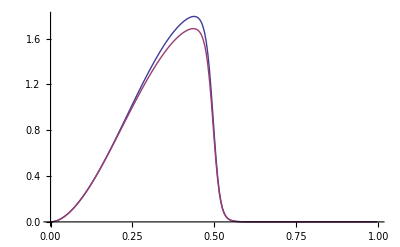

```mathematica
ListPlot[{sum,summ2},Joined->True]
```

```mathematica
NIntegrate[2Interpolation[sum][x],{x,0,Sqrt[1-(10/137)^2]}]
NIntegrate[2Interpolation[summ2][x],{x,10^-5,1-0.005}]
1
```

0.967114

0.92719

0.951372

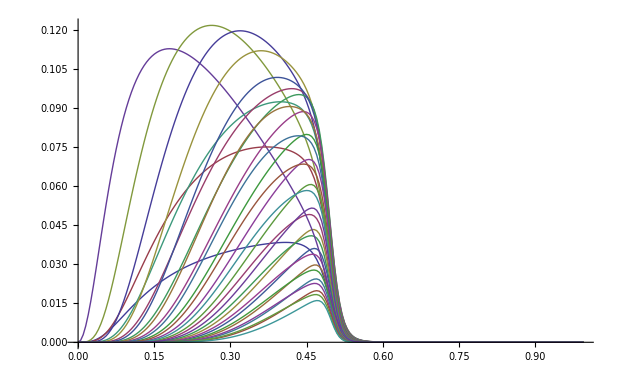

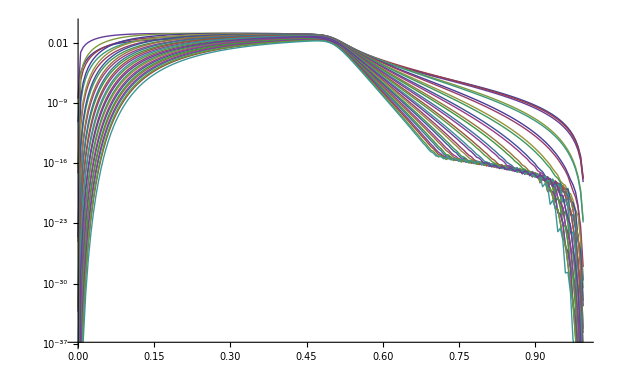

```mathematica
ListPlot[Table[res[i],{i,1,imax}], Joined->True]
ListLogPlot[Table[res[i],{i,1,imax}], Joined->True]
```

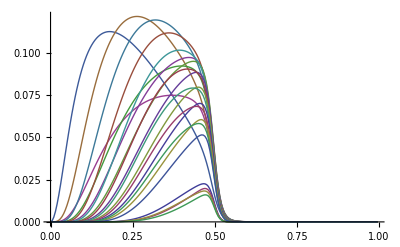

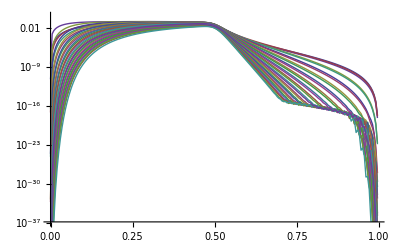

```mathematica
ListPlot[Table[res[i],{i,10,imax}], Joined->True]
ListLogPlot[Table[res[i],{i,1,imax}], Joined->True]
```

```mathematica
eexp=0.79(10/137)^5 1024/(5 Pi)(Sqrt[1-(10/137)^2]-i)^5
```

0.00010671 ((7 √381)/137-i)^5

```mathematica
tab=Table[{i,eexp},{i,0.95,1,0.001}];
```

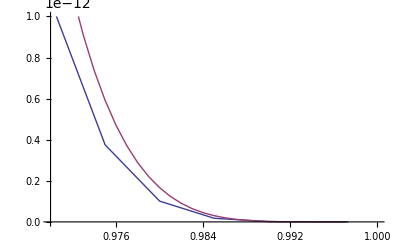

```mathematica
ListPlot[{sum,tab},PlotRange->{{0.97,1},{0,10^-12}},Joined->True]
```